```mathematica
((Abs[(1-z)]^2G4d-(Abs[(1-z)]^2G4d/.z->1-z)/.Δ->s+2/.s->i))
```

-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]])

```mathematica
crossing4d[n_]:=Abs[(1-z)]^2-Abs[(z)]^2+Sum[C[i](((Abs[(1-z)]^2G4d-(Abs[(1-z)]^2G4d/.z->1-z)/.Δ->Δ[i]/.s->s[i]))),{i,0,n}]
```

```mathematica
crossing4dRealz[n_]:=Abs[(1-z)]^2-Abs[(z)]^2+Sum[C[i](1/4 ((1-z)^Δ z^2 ((-1+z) (2+s-Δ) Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-1-s+Δ,1-z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]-Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,1-z] (4 (1+s) Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]-(-1+z) (s+Δ) Hypergeometric2F1[1/2 (2+s+Δ),1/2 (2+s+Δ),1+s+Δ,1-z]))+z^Δ Abs[1-z]^2 (z (2+s-Δ) Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-1-s+Δ,z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]+Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,z] (4 (1+s) Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]+z (s+Δ) Hypergeometric2F1[1/2 (2+s+Δ),1/2 (2+s+Δ),1+s+Δ,z]))))/.Δ->Δ[i]/.s->s[i],{i,0,n}]
```

```mathematica
Normal[Series[Simplify[Abs[(1-z)]^2G4d-(Abs[(1-z)]^2G4d/.z->1-z)/.z->r Exp[I θ],r>0&&θ>0],{θ,0,0}]]/.θ->0/.r->z//Simplify
```

1/4 ((1-z)^Δ z^2 ((-1+z) (2+s-Δ) Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-1-s+Δ,1-z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]-Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,1-z] (4 (1+s) Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]-(-1+z) (s+Δ) Hypergeometric2F1[1/2 (2+s+Δ),1/2 (2+s+Δ),1+s+Δ,1-z]))+z^Δ Abs[1-z]^2 (z (2+s-Δ) Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-1-s+Δ,z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]+Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,z] (4 (1+s) Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]+z (s+Δ) Hypergeometric2F1[1/2 (2+s+Δ),1/2 (2+s+Δ),1+s+Δ,z])))

```mathematica
crossing4dsusy[n_]:=Abs[(1-z)]^2-Abs[(z)]^2+Sum[C[i]((-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]]))),{i,0,n}]
```

```mathematica
crossing4dsusyRealz[n_]:=Abs[(1-z)]^2-Abs[(z)]^2+Sum[C[i](-1/2 (1+i) (1-z)^(1+i) (-1+z) z^2 (-2 Hypergeometric2F1[1+i,1+i,2+2 i,1-z]-Hypergeometric2F1[2+i,2+i,3+2 i,1-z]+z Hypergeometric2F1[2+i,2+i,3+2 i,1-z])+1/2 (1+i) z^(2+i) Abs[1-z]^2 (2 Hypergeometric2F1[1+i,1+i,2+2 i,z]+z Hypergeometric2F1[2+i,2+i,3+2 i,z])),{i,0,n}]
```

```mathematica
crossing4dsusyResc[n_]:=Abs[(1-z)]^2-Abs[(z)]^2+Sum[C[i]((-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]])))Exp[-137/100*Δ[i]]/.Δ[i]->i+2,{i,0,n}]
```

```mathematica
N[Log[((-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]])))]/.z->4/10+ϵ I/.ϵ->1/10000/.i->100,50]
```

-7.8187502934617610819540976226862329645950072516959+3.141592653589793238462643383279502884197169399375 ⅈ

```mathematica
Normal[Series[Simplify[((-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]])))/.z->r Exp[I θ],r>0&&θ>0],{θ,0,0}]]/.θ->0/.r->z
```

-1/2 (1+i) (1-z)^(1+i) (-1+z) z^2 (-2 Hypergeometric2F1[1+i,1+i,2+2 i,1-z]-Hypergeometric2F1[2+i,2+i,3+2 i,1-z]+z Hypergeometric2F1[2+i,2+i,3+2 i,1-z])+1/2 (1+i) z^(2+i) Abs[1-z]^2 (2 Hypergeometric2F1[1+i,1+i,2+2 i,z]+z Hypergeometric2F1[2+i,2+i,3+2 i,z])

```mathematica
zvalsTable[min_,max_,n_]:=Table[{z->i},{i,min,max,(-min+max)/n}]
```

```mathematica
solns[rul_,eqs_,nstates_,WP_]:=Block[{$MaxExtraPrecision=1000,idx},idx=Range[Length[eqs]];Table[Solve[Table[N[eqs[[idx[[i+nstates j]]]]==0/.rul,WP]//Chop,{i,nstates}],WorkingPrecision->WP][[1]],{j,0,9}]];
```

```mathematica
getAvCs[nstates_,deltas_,spins_,zmin_,zmax_,dσ_,WP_]:=Module[{cs,eqs},eqs=crossing4dRealz[nstates-1]/.C[j_]-> c[j]/.Δσ->dσ/.zvalsTable[zmin,zmax,nstates*10-1];cs=Table[N[c[i],WP],{i,0,nstates-1}]/.solns[Table[{Δ[i]->deltas[[i+1]],s[i]->spins[[i+1]]},{i,0,nstates-1}]//Flatten,eqs,nstates,WP];
Table[{Mean[cs[[;;,i]]],StandardDeviation[cs[[;;,i]]]},{i,Length[cs[[1]]]}]]
```

```mathematica
solns[Table[{Δ[i]->Table[2i,{i,6}][[i+1]],s[i]->Table[2i,{i,6}][[i+1]]},{i,0,5-1}]//Flatten,crossing4dRealz[5-1]/.C[j_]-> c[j]/.Δσ->1/.zvalsTable[4/10,49/100,5*10-1],5,40]
```

$Aborted

```mathematica
Table[{Δ[i]->Table[2i,{i,6}][[i+1]],s[i]->Table[2i,{i,6}][[i+1]]},{i,0,5-1}]//Flatten
```

{Δ[0]→2,s[0]→2,Δ[1]→4,s[1]→4,Δ[2]→6,s[2]→6,Δ[3]→8,s[3]→8,Δ[4]→10,s[4]→10}

```mathematica
crossing4dRealz[5-1]/.C[j_]-> c[j]/.Δσ->1/.zvalsTable[4/10,49/100,5*10-1]/.{Δ[0]->2,s[0]->2,Δ[1]->4,s[1]->4,Δ[2]->6,s[2]->6,Δ[3]->8,s[3]->8,Δ[4]->10,s[4]->10}
```

```mathematica
getAvCs[5,Table[2i,{i,0,6}],Table[2i,{i,0,6}],4/10,49/100,1,40]
```

{{0.66903538675510479763348342268485,0.000221210131897925099623657141},{0.19869487108703813532984879569024,0.0001182194781146183914425790166},{0.016500500380749714963951023228212,0.00005152948442238250698496511571},{0.00092861106997186341827568754200314,0.0000156433781226191262540654632711},{0.00013997820789087628043085109988682,2.35317240360393284789120986052×10^-6}}

```mathematica
getAvCs[5,Table[2i,{i,6}],Table[2i,{i,0,6}],4/10,49/100,1,40]
```

{{2.0123993120223663615533985169786,0.001156668322138356064966664001},{0.32952655488284139960406959549093,0.0003449695815813685976635469762},{0.030051932425460831436465029013499,0.00012173262705743753877461498869},{0.0016591509306967841945427351758818,0.0000334584333806005058130217374842},{0.0002711509820430933483805916909359,4.74585170426437006043342803067×10^-6}}

```mathematica
Table[{Δ[i]->Table[2i,{i,6}][[i+1]],s[i]->Table[2i,{i,0,6}][[i+1]]},{i,0,5-1}]//Flatten
```

{Δ[0]→2,s[0]→0,Δ[1]→4,s[1]→2,Δ[2]→6,s[2]→4,Δ[3]→8,s[3]→6,Δ[4]→10,s[4]→8}

```mathematica
crossing4dRealz[4]/.{Δ[0]->2,s[0]->2,Δ[1]->4,s[1]->4,Δ[2]->6,s[2]->6,Δ[3]->8,s[3]->8,Δ[4]->10,s[4]->10}/.C[i_]->%621[[i+1,1]]/.z->3/10
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

3.33765693769341438533483×10^-7

```mathematica
crossing4dRealz[4]/.{Δ[0]->2,s[0]->0,Δ[1]->4,s[1]->2,Δ[2]->6,s[2]->4,Δ[3]->8,s[3]->6,Δ[4]->10,s[4]->8}/.C[i_]->%628[[i+1,1]]/.z->4/10
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

8.17720674269090447018×10^-11

Part::pkspec1: The expression 1+i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

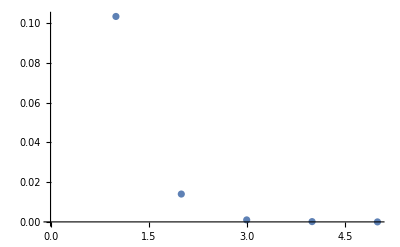

```mathematica
ListPlot[Table[crossing4dRealz[n]/.{Δ[0]->2,s[0]->0,Δ[1]->4,s[1]->2,Δ[2]->6,s[2]->4,Δ[3]->8,s[3]->6,Δ[4]->10,s[4]->8}/.C[i_]->%628[[i+1,1]]/.z->4/10,{n,0,4}]]
```

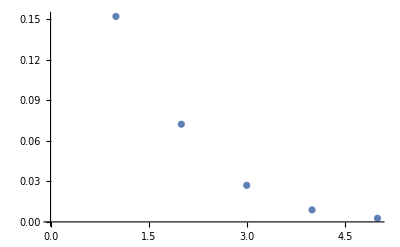

```mathematica
ListPlot[Table[crossing4dsusyRealz[n]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10,{n,0,4}]]
```

```mathematica
N[crossing4dsusyRealz[5]/.C[1]->0/.C[3]->0/.C[5]->0/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10,40]
```

0.1006031745226133813133821143493473284676

```mathematica
getAvCs[4,Table[i+2,{i,0,10}],Table[i,{i,0,10}],4/10,49/100,1,60]
```

{{-47.818474238103023210506089245244772772991512095110397,1.642113066865832943576953151622112429063473040830526},{23.274494465552127089924461826678077746263182312818684,0.7517404993443514048209936645853462947165594504161453},{-5.6566406626518967286787797365408542347612712850839398,0.1798118897604787135897329131406005296580166592948366},{0.87412811722006165275754277050913484451834410720910427,0.0211959818171602315087558648137535736507084376657353}}

```mathematica
N[crossing4dsusyRealz[5]/.C[0]->x/.C[1]->y/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10,40]
```

0.1285154149131485595739142097222585089712-0.048 x-0.1594884894707020262954486494372383014892 y

```mathematica
N[crossing4dsusyRealz[5]/.C[0]->x/.C[1]->y/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->45/100,40]
```

0.06566287854035819343358493034673717977011-0.02475 x-0.08127461093371721735830495480110449704593 y

```mathematica
crossing4dsusyRealz[5]/.C[0]->x/.C[1]->y
```

Abs[1-z]^2-Abs[z]^2+x (1/2 z^2 Abs[1-z]^2 (-(2 Log[1-z])/z+(2 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))-1/2 (1-z) (-1+z) z^2 (-(2 Log[z])/(-1+z)+(2 (1-z+z Log[z]))/(-1+z)^2-(2 (1-z+z Log[z]))/((-1+z)^2 z)))+y (z^3 Abs[1-z]^2 ((12 (-2 z-2 Log[1-z]+z Log[1-z]))/z^3-(6 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^3))-(1-z)^2 (-1+z) z^2 (-(12 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4-(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/((-1+z)^4 z)))+C[2] (3/2 z^4 Abs[1-z]^2 (-(60 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(20 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))-3/2 (1-z)^3 (-1+z) z^2 (-(60 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/(-1+z)^6-(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^6 z)))+C[3] (2 z^5 Abs[1-z]^2 ((280 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^7)-(70 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))/(3 (-1+z) z^7))-2 (1-z)^4 (-1+z) z^2 (-(280 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8)-(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8 z)))+C[4] (5/2 z^6 Abs[1-z]^2 (-(210 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(42 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))-5/2 (1-z)^5 (-1+z) z^2 (-(210 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/(-1+z)^10-(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^10 z)))+C[5] (3 z^7 Abs[1-z]^2 ((924 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^11)-(924 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z]))/(5 (-1+z) z^11))-3 (1-z)^6 (-1+z) z^2 (-(924 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12)-(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12 z)))

```mathematica
crossing4dRealz[5]/.Table[Δ[i]->2i+2,{i,0,8}]/.Table[s[i]->2i,{i,0,8}]/.C[0]->x/.C[1]->y
```

Abs[1-z]^2-Abs[z]^2+1/4 C[5] ((1-z)^12 z^2 (-44 Hypergeometric2F1[11,11,22,1-z]+22 (-1+z) Hypergeometric2F1[12,12,23,1-z])+z^12 Abs[1-z]^2 (44 Hypergeometric2F1[11,11,22,z]+22 z Hypergeometric2F1[12,12,23,z]))+1/4 x (z^2 Abs[1-z]^2 (-(4 Log[1-z])/z+(4 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))+(1-z)^2 z^2 (-(4 Log[z])/(-1+z)+(4 (1-z+z Log[z]))/((-1+z) z)))+1/4 y (z^4 Abs[1-z]^2 (-(360 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(120 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))+(1-z)^4 z^2 (-(360 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(120 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^5 z)))+1/4 C[2] (z^6 Abs[1-z]^2 (-(2100 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(420 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))+(1-z)^6 z^2 (-(2100 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(420 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^9 z)))+1/4 C[3] (z^8 Abs[1-z]^2 (-(168168 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z]))/(5 z^13)+(24024 (-120120 z+392700 z^2-492800 z^3+295820 z^4-85764 z^5+10507 z^6-353 z^7-120120 Log[1-z]+452760 z Log[1-z]-679140 z^2 Log[1-z]+514500 z^3 Log[1-z]-205800 z^4 Log[1-z]+41160 z^5 Log[1-z]-3430 z^6 Log[1-z]+70 z^7 Log[1-z]))/(5 (-1+z) z^13))+(1-z)^8 z^2 (-(168168 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13)+(24024 (10+1911 z+18228 z^2+30625 z^3-12250 z^4-30135 z^5-8036 z^6-353 z^7+490 z Log[z]+8820 z^2 Log[z]+36750 z^3 Log[z]+49000 z^4 Log[z]+22050 z^5 Log[z]+2940 z^6 Log[z]+70 z^7 Log[z]))/(5 (-1+z)^13 z)))+1/4 C[4] (z^10 Abs[1-z]^2 (-(393822 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z]))/(7 z^17)+1/(7 (-1+z) z^17)43758 (-30630600 z+130630500 z^2-229128900 z^3+212882670 z^4-112342230 z^5+33481140 z^6-5248980 z^7+363249 z^8-6989 z^9-30630600 Log[1-z]+145945800 z Log[1-z]-291891600 z^2 Log[1-z]+317837520 z^3 Log[1-z]-204324120 z^4 Log[1-z]+78586200 z^5 Log[1-z]-17463600 z^6 Log[1-z]+2041200 z^7 Log[1-z]-102060 z^8 Log[1-z]+1260 z^9 Log[1-z]))+(1-z)^10 z^2 (-(393822 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z]))/(7 (-1+z)^17)+(43758 (140+50301 z+974592 z^2+4642848 z^3+5778864 z^4-2222640 z^5-6322176 z^6-2594592 z^7-300348 z^8-6989 z^9+11340 z Log[z]+362880 z^2 Log[z]+2963520 z^3 Log[z]+8890560 z^4 Log[z]+11113200 z^5 Log[z]+5927040 z^6 Log[z]+1270080 z^7 Log[z]+90720 z^8 Log[z]+1260 z^9 Log[z]))/(7 (-1+z)^17 z)))

```mathematica
y/.Solve[%701==0,y]
```

{(4 (-Abs[1-z]^2+Abs[z]^2-1/4 C[5] ((1-z)^12 z^2 (-44 Hypergeometric2F1[11,11,22,1-z]+22 (-1+z) Hypergeometric2F1[12,12,23,1-z])+z^12 Abs[1-z]^2 (44 Hypergeometric2F1[11,11,22,z]+22 z Hypergeometric2F1[12,12,23,z]))-1/4 x (z^2 Abs[1-z]^2 (-(4 Log[1-z])/z+(4 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))+(1-z)^2 z^2 (-(4 Log[z])/(-1+z)+(4 (1-z+z Log[z]))/((-1+z) z)))-1/4 C[2] (z^6 Abs[1-z]^2 (-(2100 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(420 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))+(1-z)^6 z^2 (-(2100 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(420 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^9 z)))-1/4 C[3] (z^8 Abs[1-z]^2 (-(168168 (9240 z-23100 z^2+20720 z^3-7980 z^4+1218 z^5-49 z^6+9240 Log[1-z]-27720 z Log[1-z]+31500 z^2 Log[1-z]-16800 z^3 Log[1-z]+4200 z^4 Log[1-z]-420 z^5 Log[1-z]+10 z^6 Log[1-z]))/(5 z^13)+(24024 (-120120 z+392700 z^2-492800 z^3+295820 z^4-85764 z^5+10507 z^6-353 z^7-120120 Log[1-z]+452760 z Log[1-z]-679140 z^2 Log[1-z]+514500 z^3 Log[1-z]-205800 z^4 Log[1-z]+41160 z^5 Log[1-z]-3430 z^6 Log[1-z]+70 z^7 Log[1-z]))/(5 (-1+z) z^13))+(1-z)^8 z^2 (-(168168 (49+924 z+2625 z^2-2625 z^4-924 z^5-49 z^6+10 Log[z]+360 z Log[z]+2250 z^2 Log[z]+4000 z^3 Log[z]+2250 z^4 Log[z]+360 z^5 Log[z]+10 z^6 Log[z]))/(5 (-1+z)^13)+(24024 (10+1911 z+18228 z^2+30625 z^3-12250 z^4-30135 z^5-8036 z^6-353 z^7+490 z Log[z]+8820 z^2 Log[z]+36750 z^3 Log[z]+49000 z^4 Log[z]+22050 z^5 Log[z]+2940 z^6 Log[z]+70 z^7 Log[z]))/(5 (-1+z)^13 z)))-1/4 C[4] (z^10 Abs[1-z]^2 (-(393822 (1801800 z-6306300 z^2+8768760 z^3-6156150 z^4+2288440 z^5-429660 z^6+34632 z^7-761 z^8+1801800 Log[1-z]-7207200 z Log[1-z]+11771760 z^2 Log[1-z]-10090080 z^3 Log[1-z]+4851000 z^4 Log[1-z]-1293600 z^5 Log[1-z]+176400 z^6 Log[1-z]-10080 z^7 Log[1-z]+140 z^8 Log[1-z]))/(7 z^17)+1/(7 (-1+z) z^17)43758 (-30630600 z+130630500 z^2-229128900 z^3+212882670 z^4-112342230 z^5+33481140 z^6-5248980 z^7+363249 z^8-6989 z^9-30630600 Log[1-z]+145945800 z Log[1-z]-291891600 z^2 Log[1-z]+317837520 z^3 Log[1-z]-204324120 z^4 Log[1-z]+78586200 z^5 Log[1-z]-17463600 z^6 Log[1-z]+2041200 z^7 Log[1-z]-102060 z^8 Log[1-z]+1260 z^9 Log[1-z]))+(1-z)^10 z^2 (-(393822 (761+28544 z+208544 z^2+395136 z^3-395136 z^5-208544 z^6-28544 z^7-761 z^8+140 Log[z]+8960 z Log[z]+109760 z^2 Log[z]+439040 z^3 Log[z]+686000 z^4 Log[z]+439040 z^5 Log[z]+109760 z^6 Log[z]+8960 z^7 Log[z]+140 z^8 Log[z]))/(7 (-1+z)^17)+(43758 (140+50301 z+974592 z^2+4642848 z^3+5778864 z^4-2222640 z^5-6322176 z^6-2594592 z^7-300348 z^8-6989 z^9+11340 z Log[z]+362880 z^2 Log[z]+2963520 z^3 Log[z]+8890560 z^4 Log[z]+11113200 z^5 Log[z]+5927040 z^6 Log[z]+1270080 z^7 Log[z]+90720 z^8 Log[z]+1260 z^9 Log[z]))/(7 (-1+z)^17 z)))))/(z^4 Abs[1-z]^2 (-(360 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(120 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))+(1-z)^4 z^2 (-(360 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(120 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^5 z)))}

```mathematica
getAvCs[8,Table[2i+2,{i,0,8}],Table[2i,{i,0,8}],3/10,49/100,1,60]
```

{{1.999750961184561223323303175828587083546228977,0.0001614924614186894019578316091228887682854},{0.3334127586124525369519008829517916909437150259,0.0000509933865498338993122532763095439735254148},{0.02853626961887564919984908404658854093185984185,0.0000218411368637262100936974381496342909071536},{0.002180436460724721505953843791117181738161127957,9.256577302128081220685609798298193051352149×10^-6},{0.0001490370604763510346334197915470370364805414445,3.3008320031488450910592544216876520332906382×10^-6},{0.00001286103052147835055036573569858653023885068567,8.8392412472630363874193746544386160144716439×10^-7},{2.67691254305931847421661993194849965642907334×10^-7,1.54432419570125063015760409184206004615938×10^-7},{1.167055707335247226093869461945577852872901894×10^-7,1.306639877687655479744204870659505490182213×10^-8}}

Part::partw: Part 6 of {2,4,6,8,10} does not exist.

Part::partw: Part 6 of {0,2,4,6,8} does not exist.

Part::partw: Part 7 of {2,4,6,8,10} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
y/.Solve[crossing4dsusyRealz[5]==0/.C[0]->x/.C[1]->y,y][[1]]
```

(-Abs[1-z]^2+Abs[z]^2-x (1/2 z^2 Abs[1-z]^2 (-(2 Log[1-z])/z+(2 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))-1/2 (1-z) (-1+z) z^2 (-(2 Log[z])/(-1+z)+(2 (1-z+z Log[z]))/(-1+z)^2-(2 (1-z+z Log[z]))/((-1+z)^2 z)))-C[2] (3/2 z^4 Abs[1-z]^2 (-(60 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(20 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))-3/2 (1-z)^3 (-1+z) z^2 (-(60 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/(-1+z)^6-(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^6 z)))-C[3] (2 z^5 Abs[1-z]^2 ((280 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^7)-(70 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))/(3 (-1+z) z^7))-2 (1-z)^4 (-1+z) z^2 (-(280 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8)-(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8 z)))-C[4] (5/2 z^6 Abs[1-z]^2 (-(210 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(42 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))-5/2 (1-z)^5 (-1+z) z^2 (-(210 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/(-1+z)^10-(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^10 z)))-C[5] (3 z^7 Abs[1-z]^2 ((924 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^11)-(924 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z]))/(5 (-1+z) z^11))-3 (1-z)^6 (-1+z) z^2 (-(924 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12)-(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12 z))))/(z^3 Abs[1-z]^2 ((12 (-2 z-2 Log[1-z]+z Log[1-z]))/z^3-(6 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^3))-(1-z)^2 (-1+z) z^2 (-(12 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4-(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/((-1+z)^4 z)))

```mathematica
%702/.C[i_]->%683[[i+1,1]]/.Table[{z->2/10+i/50},{i,0,9}]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

{{(4 (-0.4766249077430052782243966681184648052244033313-1/4 x (16/625 (-25 (-1/5+4/5 Log[5/4])+20 Log[5/4])+16/625 (-25 (4/5-Log[5]/5)-5 Log[5]))))/((16 (-1125000 (27/25-121/25 Log[5/4])-468750 (-113/25+2532/125 Log[5/4])))/15625+(256 (-234375/128 (104/25-(318 Log[5])/125)+140625/128 (72/25-(46 Log[5])/25)))/15625)},{(4 (-0.4590633953590241521496107637945317122067206737-1/4 x ((184041 (-10000/429 (-11/50+39/50 Log[50/39])+200/11 Log[50/39]))/6250000+(184041 (-10000/429 (39/50-11/50 Log[50/11])-200/39 Log[50/11]))/6250000)))/((22268961 (-(112500000000 (2937/2500-(11821 Log[50/39])/2500))/161051-(625000000000 (-15059/3125+(2424357 Log[50/39])/125000))/2093663))/15625000000+(279926361 (-(625000000000 (13806/3125-(360393 Log[50/11])/125000))/330822063+(12500000000 (7137/2500-(4821 Log[50/11])/2500))/10024911))/15625000000)},{(4 (-0.4375941781500347413538665161680893627195394558-1/4 x ((12996 (-1250/57 (-6/25+19/25 Log[25/19])+50/3 Log[25/19]))/390625+(12996 (-1250/57 (19/25-6/25 Log[25/6])-100/19 Log[25/6]))/390625)))/((467856 (-48828125/108 (792/625-2886/625 Log[25/19])-(1220703125 (-15912/3125+(289902 Log[25/19])/15625))/6156))/244140625+(4691556 (-(4882812500 (14573/3125-(50598 Log[25/6])/15625))/2476099+(3515625000 (1767/625-1261/625 Log[25/6]))/2476099))/244140625)},{(4 (-0.4128952826486946071313377073014740673651031136-1/4 x ((231361 (-10000/481 (-13/50+37/50 Log[50/37])+200/13 Log[50/37]))/6250000+(231361 (-10000/481 (37/50-13/50 Log[50/13])-200/37 Log[50/13]))/6250000)))/((39100009 (-(112500000000 (3393/2500-(11269 Log[50/37])/2500))/371293-(1875000000000 (-33371/6250+(2216559 Log[50/37])/125000))/13737841))/15625000000+(316733209 (-(1875000000000 (30599/6250-(451191 Log[50/13])/125000))/901471441+(112500000000 (6993/2500-(5269 Log[50/13])/2500))/69343957))/15625000000)},{(4 (-0.38552559949480307508231256860067587852483658926-1/4 x ((15876 (-1250/63 (-7/25+18/25 Log[25/18])+100/7 Log[25/18]))/390625+(15876 (-1250/63 (18/25-7/25 Log[25/7])-50/9 Log[25/7]))/390625)))/((777924 (-(3515625000 (903/625-2749/625 Log[25/18]))/16807-(4882812500 (-17381/3125+(264546 Log[25/18])/15625))/50421))/244140625+(5143824 (-(1220703125 (15984/3125-(62454 Log[25/7])/15625))/551124+(48828125 (1728/625-1374/625 Log[25/7]))/26244))/244140625)},{(4 (-0.35594764732262899994381393919096368485551597881-1/4 x ((441 (-400/21 (-3/10+7/10 Log[10/7])+40/3 Log[10/7]))/10000+(441 (-400/21 (7/10-3/10 Log[10/3])-40/7 Log[10/3]))/10000)))/((3969 (-4000000/27 (153/100-429/100 Log[10/7])-40000000/567 (-144/25+(16149 Log[10/7])/1000)))/1000000+(21609 (-(40000000 (133/25-(4401 Log[10/3])/1000))/16807+(36000000 (273/100-229/100 Log[10/3]))/16807))/1000000)},{(4 (-0.32454607676881087105108835560896157116271952738-1/4 x ((18496 (-625/34 (-8/25+17/25 Log[25/17])+25/2 Log[25/17]))/390625+(18496 (-625/34 (17/25-8/25 Log[25/8])-100/17 Log[25/8]))/390625)))/((1183744 (-(439453125 (1008/625-2614/625 Log[25/17]))/4096-(3662109375 (-18544/3125+(240414 Log[25/17])/15625))/69632))/244140625+(5345344 (-(3662109375 (17221/3125-(75336 Log[25/8])/15625))/1419857+(3515625000 (1683/625-1489/625 Log[25/8]))/1419857))/244140625)},{(4 (-0.29164258993950698875733210711044440352841975807-1/4 x ((314721 (-10000/561 (-17/50+33/50 Log[50/33])+200/17 Log[50/33]))/6250000+(314721 (-10000/561 (33/50-17/50 Log[50/17])-200/33 Log[50/17]))/6250000)))/((90954369 (-(112500000000 (4233/2500-(10189 Log[50/33])/2500))/1419857-(625000000000 (-38029/6250+(1830411 Log[50/33])/125000))/15618427))/15625000000+(342731169 (-(625000000000 (35541/6250-(657339 Log[50/17])/125000))/221767227+(12500000000 (6633/2500-(6189 Log[50/17])/2500))/4348377))/15625000000)},{(4 (-0.25750799152140465163064396668415665953614214654-1/4 x ((20736 (-625/36 (-9/25+16/25 Log[25/16])+100/9 Log[25/16]))/390625+(20736 (-625/36 (16/25-9/25 Log[25/9])-25/4 Log[25/9]))/390625)))/((1679616 (-(390625000 (1107/625-2481/625 Log[25/16]))/6561-(1220703125 (-19413/3125+(217488 Log[25/16])/15625))/39366))/244140625+(5308416 (-(1220703125 (18272/3125-(89262 Log[25/9])/15625))/393216+(439453125 (1632/625-1606/625 Log[25/9]))/131072))/244140625)},{(4 (-0.22237199454436311850976788883110768161664605264-1/4 x ((346921 (-10000/589 (-19/50+31/50 Log[50/31])+200/19 Log[50/31]))/6250000+(346921 (-10000/589 (31/50-19/50 Log[50/19])-200/31 Log[50/19]))/6250000)))/((125238481 (-(112500000000 (4617/2500-(9661 Log[50/31])/2500))/2476099-(1875000000000 (-19741/3125+(1651773 Log[50/31])/125000))/76759069))/15625000000+(333391081 (-(1875000000000 (18724/3125-(772977 Log[50/19])/125000))/543953869+(112500000000 (6417/2500-(6661 Log[50/19])/2500))/28629151))/15625000000)}}

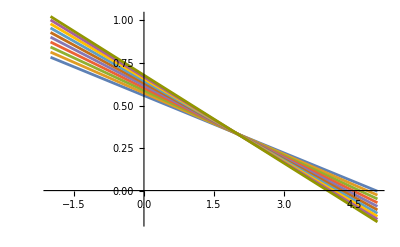

```mathematica
Plot[%,{x,-2,5},WorkingPrecision->30]
```

```mathematica
crossing4dRealz[5]/.Table[Δ[i]->2i+2,{i,0,8}]/.Table[s[i]->2i,{i,0,8}]/.C[i_]->%698[[i+1,1]]/.Table[{z->3/10+i/50},{i,0,9}]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

{5.3962177385047522998041610386017055574333×10^-6,2.8023010023922184006743027808938638974353×10^-6,1.451914659377649291858991090289242097714×10^-6,7.49408039995443790896183589922333829769×10^-7,3.847547615039062140361351501290518554831×10^-7,1.96146259217186412666702884975194807837×10^-7,9.90192592174006156746985395966816962958×10^-8,4.91511793846020564735380995912435625877×10^-8,2.33547273848463564669571730522711856838×10^-8,9.29437059851439385901752701194791820062×10^-9}

```mathematica
%683
```

{{1.999750961184561223323303175828587083546228977,0.0001614924614186894019578316091228887682854},{0.3334127586124525369519008829517916909437150259,0.0000509933865498338993122532763095439735254148},{0.02853626961887564919984908404658854093185984185,0.0000218411368637262100936974381496342909071536},{0.002180436460724721505953843791117181738161127957,9.256577302128081220685609798298193051352149×10^-6},{0.0001490370604763510346334197915470370364805414445,3.3008320031488450910592544216876520332906382×10^-6},{0.00001286103052147835055036573569858653023885068567,8.8392412472630363874193746544386160144716439×10^-7},{2.67691254305931847421661993194849965642907334×10^-7,1.54432419570125063015760409184206004615938×10^-7},{1.167055707335247226093869461945577852872901894×10^-7,1.306639877687655479744204870659505490182213×10^-8}}

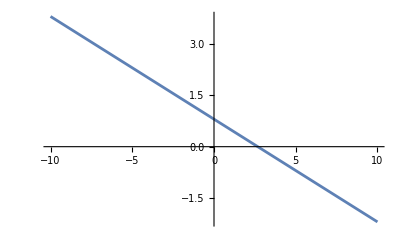

```mathematica
Plot[(-Abs[1-z]^2+Abs[z]^2-x (1/2 z^2 Abs[1-z]^2 (-(2 Log[1-z])/z+(2 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))-1/2 (1-z) (-1+z) z^2 (-(2 Log[z])/(-1+z)+(2 (1-z+z Log[z]))/(-1+z)^2-(2 (1-z+z Log[z]))/((-1+z)^2 z)))+1/6 (-3/2 z^4 Abs[1-z]^2 (-(60 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(20 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))+3/2 (1-z)^3 (-1+z) z^2 (-(60 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/(-1+z)^6-(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^6 z)))+1/20 (-2 z^5 Abs[1-z]^2 ((280 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^7)-(70 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))/(3 (-1+z) z^7))+2 (1-z)^4 (-1+z) z^2 (-(280 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8)-(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8 z)))+1/70 (-5/2 z^6 Abs[1-z]^2 (-(210 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(42 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))+5/2 (1-z)^5 (-1+z) z^2 (-(210 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/(-1+z)^10-(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^10 z)))+1/252 (-3 z^7 Abs[1-z]^2 ((924 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^11)-(924 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z]))/(5 (-1+z) z^11))+3 (1-z)^6 (-1+z) z^2 (-(924 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12)-(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12 z))))/(z^3 Abs[1-z]^2 ((12 (-2 z-2 Log[1-z]+z Log[1-z]))/z^3-(6 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^3))-(1-z)^2 (-1+z) z^2 (-(12 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4-(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/((-1+z)^4 z)))/.{{z->4/10},{z->I/4}}//Evaluate,{x,-10,10}]
```

```mathematica
N[(-Abs[1-z]^2+Abs[z]^2-x (1/2 z^2 Abs[1-z]^2 (-(2 Log[1-z])/z+(2 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))-1/2 (1-z) (-1+z) z^2 (-(2 Log[z])/(-1+z)+(2 (1-z+z Log[z]))/(-1+z)^2-(2 (1-z+z Log[z]))/((-1+z)^2 z)))+1/6 (-3/2 z^4 Abs[1-z]^2 (-(60 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+(20 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))/((-1+z) z^5))+3/2 (1-z)^3 (-1+z) z^2 (-(60 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/(-1+z)^6-(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^6 z)))+1/20 (-2 z^5 Abs[1-z]^2 ((280 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 z^7)-(70 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))/(3 (-1+z) z^7))+2 (1-z)^4 (-1+z) z^2 (-(280 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8)-(70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z]))/(3 (-1+z)^8 z)))+1/70 (-5/2 z^6 Abs[1-z]^2 (-(210 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z]))/z^9+(42 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))/((-1+z) z^9))+5/2 (1-z)^5 (-1+z) z^2 (-(210 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z]))/(-1+z)^9+(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/(-1+z)^10-(42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z]))/((-1+z)^10 z)))+1/252 (-3 z^7 Abs[1-z]^2 ((924 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z]))/(5 z^11)-(924 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z]))/(5 (-1+z) z^11))+3 (1-z)^6 (-1+z) z^2 (-(924 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z]))/(5 (-1+z)^11)+(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12)-(924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))/(5 (-1+z)^12 z))))/(z^3 Abs[1-z]^2 ((12 (-2 z-2 Log[1-z]+z Log[1-z]))/z^3-(6 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^3))-(1-z)^2 (-1+z) z^2 (-(12 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4-(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/((-1+z)^4 z)))/.{z->1/3+I/4},40]//Expand
```

(0.245390743810050293335797777705588725183+0.585017708845464617910831987343974011167 ⅈ)-(0.44912310932388461601855854501786347234+0.050450188656092061463380666960065756707 ⅈ) x

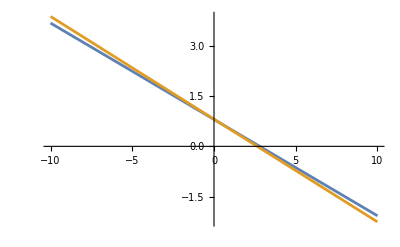

```mathematica
Plot[(-Abs[1-z]^2+Abs[z]^2-x (1/2 z^2 Abs[1-z]^2 (-(2 Log[1-z])/z+(2 (-z-Log[1-z]+z Log[1-z]))/((-1+z) z))-1/2 (1-z) (-1+z) z^2 (-(2 Log[z])/(-1+z)+(2 (1-z+z Log[z]))/(-1+z)^2-(2 (1-z+z Log[z]))/((-1+z)^2 z)))+1/6 (-3/2 z^4 Abs[1-z]^2 (-(60 (6 z-3 z^2+6 Log[1-z]-6 z Log[1-z]+z^2 Log[1-z]))/z^5+1/((-1+z) z^5)20 (-30 z+39 z^2-10 z^3-30 Log[1-z]+54 z Log[1-z]-27 z^2 Log[1-z]+3 z^3 Log[1-z]))+3/2 (1-z)^3 (-1+z) z^2 (-(60 (3-3 z^2+Log[z]+4 z Log[z]+z^2 Log[z]))/(-1+z)^5+(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/(-1+z)^6-(20 (1+18 z-9 z^2-10 z^3+9 z Log[z]+18 z^2 Log[z]+3 z^3 Log[z]))/((-1+z)^6 z)))+1/20 (-2 z^5 Abs[1-z]^2 (1/(3 z^7)280 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z])-1/(3 (-1+z) z^7)70 (420 z-750 z^2+380 z^3-47 z^4+420 Log[1-z]-960 z Log[1-z]+720 z^2 Log[1-z]-192 z^3 Log[1-z]+12 z^4 Log[1-z]))+2 (1-z)^4 (-1+z) z^2 (-(280 (11+27 z-27 z^2-11 z^3+3 Log[z]+27 z Log[z]+27 z^2 Log[z]+3 z^3 Log[z]))/(3 (-1+z)^7)+1/(3 (-1+z)^8)70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z])-1/(3 (-1+z)^8 z)70 (3+128 z+108 z^2-192 z^3-47 z^4+48 z Log[z]+216 z^2 Log[z]+144 z^3 Log[z]+12 z^4 Log[z])))+1/70 (-5/2 z^6 Abs[1-z]^2 (-1/z^9 210 (420 z-630 z^2+260 z^3-25 z^4+420 Log[1-z]-840 z Log[1-z]+540 z^2 Log[1-z]-120 z^3 Log[1-z]+6 z^4 Log[1-z])+1/((-1+z) z^9)42 (-3780 z+8610 z^2-6510 z^3+1805 z^4-131 z^5-3780 Log[1-z]+10500 z Log[1-z]-10500 z^2 Log[1-z]+4500 z^3 Log[1-z]-750 z^4 Log[1-z]+30 z^5 Log[1-z]))+5/2 (1-z)^5 (-1+z) z^2 (-1/(-1+z)^9 210 (25+160 z-160 z^3-25 z^4+6 Log[z]+96 z Log[z]+216 z^2 Log[z]+96 z^3 Log[z]+6 z^4 Log[z])+1/(-1+z)^10 42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z])-1/((-1+z)^10 z)42 (6+475 z+1400 z^2-600 z^3-1150 z^4-131 z^5+150 z Log[z]+1200 z^2 Log[z]+1800 z^3 Log[z]+600 z^4 Log[z]+30 z^5 Log[z])))+1/252 (-3 z^7 Abs[1-z]^2 (1/(5 z^11)924 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z])-1/(5 (-1+z) z^11)924 (13860 z-38430 z^2+38640 z^3-16905 z^4+2982 z^5-142 z^6+13860 Log[1-z]-45360 z Log[1-z]+56700 z^2 Log[1-z]-33600 z^3 Log[1-z]+9450 z^4 Log[1-z]-1080 z^5 Log[1-z]+30 z^6 Log[1-z]))+3 (1-z)^6 (-1+z) z^2 (-1/(5 (-1+z)^11)924 (137+1625 z+2000 z^2-2000 z^3-1625 z^4-137 z^5+30 Log[z]+750 z Log[z]+3000 z^2 Log[z]+3000 z^3 Log[z]+750 z^4 Log[z]+30 z^5 Log[z])+1/(5 (-1+z)^12)924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z])-1/(5 (-1+z)^12 z)924 (5+642 z+3750 z^2+2000 z^3-4125 z^4-2130 z^5-142 z^6+180 z Log[z]+2250 z^2 Log[z]+6000 z^3 Log[z]+4500 z^4 Log[z]+900 z^5 Log[z]+30 z^6 Log[z]))))/(z^3 Abs[1-z]^2 ((12 (-2 z-2 Log[1-z]+z Log[1-z]))/z^3-(6 (6 z-5 z^2+6 Log[1-z]-8 z Log[1-z]+2 z^2 Log[1-z]))/((-1+z) z^3))-(1-z)^2 (-1+z) z^2 (-(12 (2-2 z+Log[z]+z Log[z]))/(-1+z)^3+(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/(-1+z)^4-(6 (1+4 z-5 z^2+4 z Log[z]+2 z^2 Log[z]))/((-1+z)^4 z)))/.{{z->30/100},{z->49/100}}//Evaluate,{x,-10,10}]
```

```mathematica
Solve[%==0&&%%==0]
```

{{x→0.5943172881539438565691186465475503742909,y→0.6269304161923675708696453233548080209597}}

```mathematica
{C[0]->x,C[1]->y}/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}
```

{1→x,1/2→y}

```mathematica
N[crossing4dsusyRealz[3]/.Table[C[i]->%655[[i+1,1]],{i,0,3}]/.z->4/10,40]
```

2.859319163729650742492137745748040774996×10^-8

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],Table[2i,{i,0,4}],3/10,49/100,1,60]
```

{{1.928844639116568772564435674132202903402022722579609603,0.024130756710328890743535080024148790708470010810915659},{0.3540334834164697159147059796342628144014713049115058127,0.0065974892908536214312362752032347243410848517692812111},{0.02180010405932664420869755104307825743637825159467123149,0.00176418029073897645471690980685715842749165379901648035},{0.003761708361844936699819457356025080060954288264768253096,0.000256030540685308330910106771447628955216393018854530417}}

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],Table[2i,{i,0,4}],4/10,49/100,1,60]
```

{{1.947305350900863160191817081432147117150971069933830586,0.004050836089223879675999605966587277656324654036842305},{0.3489559425177082358759210121062007463020709338771959757,0.001140717861353950231300189717647958558343769933441942},{0.02317870489349909513595242943424971928178961884888264035,0.0003299446867001785849575692027634040204590535494110564},{0.003557111890386380761575212463913291082839538221875819714,0.00005411619063861865592401250070884070930217429947662246}}

```mathematica
getAvCs[4,Table[2i+2,{i,0,4}],Table[2i,{i,0,4}],45/100,49/100,1,60]
```

{{1.9507238955704911413785781334227156012497130636474045,0.00089292337627782567959323907792419237009574390859102},{0.347992247170625645249876605067183327053721120932386197,0.00025289837297457527827176001147979201664859359278633},{0.0234583068447419134514058845364552398054896097988828844,0.0000743845851747521175377500398715517058808189460357462},{0.00351101072838161633444231766978870103857816299966012586,0.0000125619504853110847075312277757833120882201351641031}}

```mathematica
Inverse[%351]
```

{{-5.604708314921837375131027249682800107818×10^8,1.445397265230287071475296901588616677827×10^9,-1.521368226874447832276508348770863829248×10^9,8.706022577331389928060033725783532688271×10^8,-2.701390299005819223552384015851449000304×10^8,3.597656966692044484619610777181782877101×10^7},{2.73475124230251473095432554523870129524×10^8,-7.051903883882840635713761923867260159063×10^8,7.421266365048514649394051892875572792145×10^8,-4.245792007475039249779385043960638214509×10^8,1.317019989827352772301925594190892797877×10^8,-1.753318376295186062871632958642772357871×10^7},{-8.291651201437997307381650020674463979343×10^7,2.137279990270310320984218786752311539088×10^8,-2.247790405005851964691347337573934016767×10^8,1.284853101463590714222823272260777743548×10^8,-3.981078996457673842435515354618975681147×10^7,5.292733615511876442885240214942155526163×10^6},{1.928782447706204474508775563578994087882×10^7,-4.966896718205880155243781043710293545334×10^7,5.215469309588234897279276461811454889107×10^7,-2.974756812650351066314550899356764243254×10^7,9.192245080492589301430476398174898341251×10^6,-1.218154469863072786271618767585985775174×10^6},{-3.142534909965756201696034556496423301212×10^6,8.077008037640064415897956522372213153686×10^6,-8.454925958935375893304078812458235616549×10^6,4.802324727542423428901839859444210698863×10^6,-1.476383691177804144308441205484007889196×10^6,194499.2980109008863748818984083761248709},{267510.9798526312885244384246277049317204,-685237.1531475882403455733651377715651536,713458.0168375153421233921115326730588393,-402409.9816153538353832104486827187272221,122696.5362466534827957078861451594090681,-16017.10596976851629554056703774431738702}}

```mathematica
N[crossing4dsusy[5]/.C[i_]->0/.zvals20[[;;6]],40]
```

{-0.1,-0.1,-0.1,-0.1,-0.1,-0.1}

```mathematica
RandomChoice[zvals20,6]
```

{{z→11/20+(87 ⅈ)/500},{z→21/20+(203 ⅈ)/500},{z→13/20+(116 ⅈ)/125},{z→1351079888211149/2251799813685248+(319 ⅈ)/500},{z→11/20+(87 ⅈ)/500},{z→21/20+(203 ⅈ)/500}}

```mathematica
Table[{z->4/10+I/100+x/10},{x,0,9}]
```

{{z→2/5+ⅈ/100},{z→1/2+ⅈ/100},{z→3/5+ⅈ/100},{z→7/10+ⅈ/100},{z→4/5+ⅈ/100},{z→9/10+ⅈ/100},{z→1+ⅈ/100},{z→11/10+ⅈ/100},{z→6/5+ⅈ/100},{z→13/10+ⅈ/100}}

```mathematica
Inverse[%]. N[crossing4dsusy[10]/.C[i_]->0/.{{z->7/10+(87 ⅈ)/125},{z->19/20+(203 ⅈ)/500},{z->21/20+(261 ⅈ)/500},{z->675539944105573/750599937895081+(377 ⅈ)/500},{z->11/20+(87 ⅈ)/250},{z->19/20+(261 ⅈ)/500},{z->7/10+(29 ⅈ)/250},{z->1+(58 ⅈ)/125},{z->19/20+(87 ⅈ)/250},{z->19/20+(58 ⅈ)/125},{z->13/20+(377 ⅈ)/500}},40]
```

{-1046.1499047944390552229057505173,520.569099328792334523129213592272,-171.873321920606841644561112760338,49.8710740617220752662696721018323,-13.339274833011211008159675993042,3.25512213024588672655882308491298,-0.717221507708726145953518792382345,0.136296047518761457490704978838546,-0.0214757977991511216017819934548301,0.00247664495566371866556800149067335,-0.000177539912631595803316261059480496}

```mathematica
RandomChoice[zvals20,11]
```

{{z→7/10+(87 ⅈ)/125},{z→19/20+(203 ⅈ)/500},{z→21/20+(261 ⅈ)/500},{z→675539944105573/750599937895081+(377 ⅈ)/500},{z→11/20+(87 ⅈ)/250},{z→19/20+(261 ⅈ)/500},{z→7/10+(29 ⅈ)/250},{z→1+(58 ⅈ)/125},{z→19/20+(87 ⅈ)/250},{z→19/20+(58 ⅈ)/125},{z→13/20+(377 ⅈ)/500}}

```mathematica
crossing4dsusy[10]
```

```mathematica
Table[{z->1/2-i/160},{i,16}]//N
```

{{z→0.49375},{z→0.4875},{z→0.48125},{z→0.475},{z→0.46875},{z→0.4625},{z→0.45625},{z→0.45},{z→0.44375},{z→0.4375},{z→0.43125},{z→0.425},{z→0.41875},{z→0.4125},{z→0.40625},{z→0.4}}

```mathematica
Inverse[%549].%
```

{1.32511990456×10^7,-6.61697502464×10^6,2.19422891372×10^6,-648971.775739,179785.327753,-47149.4281237,11675.7496363,-2704.64964432,577.807603993,-111.728649763,19.0896452332,-2.79222306681,0.334613695861,-0.0307250886147,0.0019188271951,-0.0000611717405251}

```mathematica
crossing4dsusyRealz[15]/.C[i_]->0/.Table[{z->1/2-i/160},{i,16}]
```

{1/80,1/40,3/80,1/20,1/16,3/40,7/80,1/10,9/80,1/8,11/80,3/20,13/80,7/40,3/16,1/5}

```mathematica
N[D[crossing4dsusyRealz[15],{Table[C[i],{i,0,15}],1}]/.Table[{z->1/2-i/160},{i,16}],100]
```

```mathematica
N[crossing4dsusyRealz[10]/.z->4/10/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1},30]
```

1.01299142388456343757276152024×10^-6

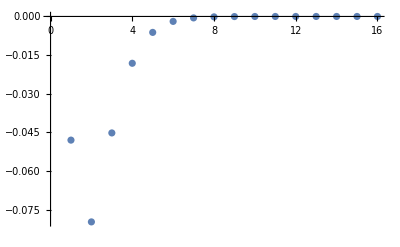

```mathematica
ListPlot@N[DiagonalMatrix[Table[C[i],{i,0,15}]].D[crossing4dsusyRealz[15],{Table[C[i],{i,0,15}],1}]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10,40]
```

```mathematica
crossing4d[5]/.C[i_]->0/.Table[{z->1/2-i/60+I/100},{i,6}]
```

{1/30,1/15,1/10,2/15,1/6,1/5}

```mathematica
Inverse[%].%579
```

{-1.997206007969069020982696171908392051379,-0.334209833630665080361346005263588258182,-0.0282048259378983564479577109363522293625,-0.0023111533470827788542028026399476334433,-0.0001092982405322689859904834076653876204,-0.00002015166652185549883600768835773232465}

```mathematica
Table[C[i]->%582[[i-1]],{i,6}]
```

{C[1]→List,C[2]→-1.997206007969069020982696171908392051379,C[3]→-0.334209833630665080361346005263588258182,C[4]→-0.0282048259378983564479577109363522293625,C[5]→-0.0023111533470827788542028026399476334433,C[6]→-0.0001092982405322689859904834076653876204}

```mathematica
N[crossing4d[5]/.Δ[i_]->s[i]+2/.s[i_]->2i/.C[i_]->Rationalize[%582[[i+1]],0]/.z->4/10+I/100,40]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

0.4+0. ⅈ

```mathematica
N[D[crossing4d[5]/.Δ[i_]->s[i]+2/.s[i_]->2i,{Table[C[i],{i,0,5}],1}]/.Table[{z->1/2-i/60+I/100},{i,6}],50]
```

{{-0.0083274172909754156552201770537542048320808460245417+0. ⅈ,-0.04443037371066320134285557329503620914545274276221+0. ⅈ,-0.060785691537389431266422889630874143609990347708974+0. ⅈ,-0.057387019175550933987168648185919166464596973071266+0. ⅈ,-0.045418639220411196146807971739390759399992639278458+0. ⅈ,-0.032426837467877312385514588324426988057376401534583+0. ⅈ},{-0.016599338592349928806915392813081229194024180650368+0. ⅈ,-0.089000214502557690246466947478850751492901550461336+0. ⅈ,-0.12345688910600665745165077936779732226519259525035+0. ⅈ,-0.11918676017632816301213568328918742063289661107195+0. ⅈ,-0.097245182231622368431157630950096060017837658891545+0. ⅈ,-0.072120319215551499364020742659886397688745086802738+0. ⅈ},{-0.024760269250602500432895565598092347824685027033244+0. ⅈ,-0.13384468093668610228202730337632132835276564790206+0. ⅈ,-0.18992606235758529093429835581323393712185185901341+0. ⅈ,-0.19005808281911610810074259859961120984014361891608+0. ⅈ,-0.16261922279022927556321119528708876544492157168794+0. ⅈ,-0.12773368006206051583535199239715131260091406921128+0. ⅈ},{-0.03275471734778286131938273541321391864312876565154+0. ⅈ,-0.17909021237702331607050602957897937075188553115742+0. ⅈ,-0.2621594542692661930009335724309959908329315331739+0. ⅈ,-0.27516320632902646913167878867076174046867415770918+0. ⅈ,-0.25021663121171537116075009384216629746949999094373+0. ⅈ,-0.21093020365715086170178200597455945127741735605268+0. ⅈ},{-0.040527195233034926160694229107343409432530381946111+0. ⅈ,-0.22484990978926600821181130722250417101494690724035+0. ⅈ,-0.34220353916895870070764763359061690666122093534645+0. ⅈ,-0.38044755956271426350416075755060376817673905514597+0. ⅈ,-0.37120706411268487945009068179935265433760840754879+0. ⅈ,-0.33851946284864558040905251402414060438593211740317+0. ⅈ},{-0.048022221265857205300171557539748561775718588556219+0. ⅈ,-0.27121859293053420428203014379434570885960832363329+0. ⅈ,-0.43221083821695672880548051380779747195949407322421+0. ⅈ,-0.51295474221238529418498757843253582459236384162475+0. ⅈ,-0.54045944805424981787770994930657903788686611158535+0. ⅈ,-0.53546710101929464226620648268896767715104339740688+0. ⅈ}}

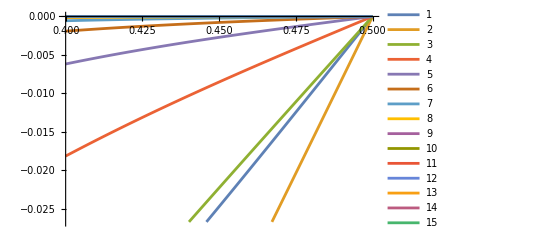

```mathematica
Plot[DiagonalMatrix[Table[C[i],{i,0,15}]].D[crossing4dsusyRealz[15],{Table[C[i],{i,0,15}],1}]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}//Evaluate,{z,4/10,1/2},PlotLegends->Automatic]
```

```mathematica
N[crossing4dsusy[15]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10+I/100,40]
```

9.541712258760039234430747174510852394101×10^-10+0. ⅈ

```mathematica
N[crossing4dsusy[12]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.z->4/10+I/100,40]
```

6.32338150918368309123166698085205146307×10^-8+0. ⅈ

```mathematica
N[crossing4dsusy[10]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1}/.zvals20,30]
```

{-1.06665000496141879534211473105×10^-7+0. ⅈ,4.14718266767539467571735002666×10^-8+0. ⅈ,3.80391590502822072128239409467×10^-8+0. ⅈ,-5.56947623227267073029015000256×10^-8+0. ⅈ,-4.29433647024376473412765169209×10^-8+0. ⅈ,8.68009621625837935411997306174×10^-8+0. ⅈ,1.28546707799679894580087170423×10^-7+0. ⅈ,-6.46082656736443595630464858294×10^-8+0. ⅈ,-3.59405474905433816201592092015×10^-7+0. ⅈ,-4.06533160791987190077208876864×10^-7+0. ⅈ,7.84107752492963694652652993365×10^-8+0. ⅈ,1.0427407683330327120123965992×10^-6+0. ⅈ,2.01169062032845574840733593628×10^-6+0. ⅈ,2.23116060797173598953728455876×10^-6+0. ⅈ,9.63113821580779752906729162232×10^-7+0. ⅈ,-2.1888448086518704586055425701×10^-6+0. ⅈ,-7.03321628254298569267621204103×10^-6+0. ⅈ,-0.000012688708966240070114832520866+0. ⅈ,-0.0000176423115272096622240682630784+0. ⅈ,-5.35314359176193903796435781659×10^-7+0. ⅈ,1.77575832902825354885120590072×10^-7+0. ⅈ,1.91260615647565915101025663588×10^-7+0. ⅈ,-2.09313707112050369266089168634×10^-7+0. ⅈ,-2.01305015509488540516345227994×10^-7+0. ⅈ,2.59957597790871151703398141521×10^-7+0. ⅈ,4.59162833826484945035025888514×10^-7+0. ⅈ,-7.95366545078467139040364329098×10^-8+0. ⅈ,-9.62434646496954286137863668179×10^-7+0. ⅈ,-1.21518236597619503687680367674×10^-6+0. ⅈ,-8.70868073016968604847687417562×10^-8+0. ⅈ,2.28693858495512616550588712098×10^-6+0. ⅈ,4.75245142382827220773023145803×10^-6+0. ⅈ,5.53751680026503942947294196756×10^-6+0. ⅈ,2.95918868676375374193704857288×10^-6+0. ⅈ,-3.85622401980796957758354572401×10^-6+0. ⅈ,-0.0000144666335460837984994998977675+0. ⅈ,-0.0000269379116495401023246038707736+0. ⅈ,-0.0000380087593850578166285034103291+0. ⅈ,-2.41198535597811021461855974512×10^-6+0. ⅈ,7.31044407810288095879346628825×10^-7+0. ⅈ,8.18214086591422752908397994136×10^-7+0. ⅈ,-7.41187925954535732210782576416×10^-7+0. ⅈ,-7.79262856949971259967044606848×10^-7+0. ⅈ,7.13823042278629754810131804318×10^-7+0. ⅈ,1.4261267954061390785626710945×10^-6+0. ⅈ,7.1761825593201224023387411264×10^-8+0. ⅈ,-2.22706406790759951823179717928×10^-6+0. ⅈ,-3.0983475718135807434575799868×10^-6+0. ⅈ,-9.05735188240279614496034712154×10^-7+0. ⅈ,3.98921699591681004541062672769×10^-6+0. ⅈ,9.2149540336072639080438271001×10^-6+0. ⅈ,0.0000113608904263819238455742896287+0. ⅈ,7.35385480292850486629935437029×10^-6+0. ⅈ,-4.29748849183593808136810763958×10^-6+0. ⅈ,-0.0000227314056894619427599946771363+0. ⅈ,-0.0000445606602118841299108002259404+0. ⅈ,-0.0000102250481445217141561174255278+0. ⅈ,3.14117642676672202187852360018×10^-6+0. ⅈ,3.12194030056452806675711127553×10^-6+0. ⅈ,-2.71782265946021191019970665577×10^-6+0. ⅈ,-2.66329387750214384011433999251×10^-6+0. ⅈ,2.08851349735488793848149333858×10^-6+0. ⅈ,4.16832154428026598479839123199×10^-6+0. ⅈ,6.3024538968114785917388340787×10^-7+0. ⅈ,-5.1040868986778699981902243042×10^-6+0. ⅈ,-7.44267061288616850456921279787×10^-6+0. ⅈ,-3.16946252315139683674516196157×10^-6+0. ⅈ,6.58857274138370218157630064409×10^-6+0. ⅈ,0.0000170555076016888495774980046974+0. ⅈ,0.0000220094614344159284362300664499+0. ⅈ,0.0000162625009381756275855051621798+0. ⅈ,-2.42205216144532999790366075379×10^-6+0. ⅈ,-0.0000323593282134481721913525581307+0. ⅈ,-0.0000679533359264868671091918332664+0. ⅈ,-0.0000413304017125293082570042154613+0. ⅈ,0.0000142908962225826814564528145727+0. ⅈ,0.0000105096468844004448924904872344+0. ⅈ,-0.0000104238795337240048795235351311+0. ⅈ,-8.08345439924389520722978981458×10^-6+0. ⅈ,6.75548981284457741361702470284×10^-6+0. ⅈ,0.0000116421948754669957707366275337+0. ⅈ,1.83998186112880698377053174197×10^-6+0. ⅈ,-0.0000119998382291648458876785025701+0. ⅈ,-0.0000172183428972485355514120326543+0. ⅈ,-8.34053750275100268146497473769×10^-6+0. ⅈ,0.0000110569812799771027480026520054+0. ⅈ,0.0000313371739115005702263679642038+0. ⅈ,0.0000414612944592793320946213614766+0. ⅈ,0.000033141393840216251513074593728+0. ⅈ,3.47225448893438154036688985779×10^-6+0. ⅈ,-0.0000441553832754416347457460894746+0. ⅈ,-0.000100608138240270130676007285457+0. ⅈ,-0.000159496580840078806495197668964+0. ⅈ,0.0000677843835648606879516609137653+0. ⅈ,0.0000284366512832743402757902753665+0. ⅈ,-0.0000405461295233675304149089183395+0. ⅈ,-0.0000206829063119905521467451510496+0. ⅈ,0.0000234175325767380892479788120659+0. ⅈ,0.0000309009654332119143830064392541+0. ⅈ,2.8334729482652137527484498065×10^-6+0. ⅈ,-0.0000291527437981791535350338417805+0. ⅈ,-0.0000386404347998707065261180987385+0. ⅈ,-0.0000187816959190215786750266330049+0. ⅈ,0.0000198361449575470653107813522186+0. ⅈ,0.000057980399712100525509206635249+0. ⅈ,0.0000767122593165330798247570354004+0. ⅈ,0.0000636392237877095869406378803774+0. ⅈ,0.0000159055024955171419836902119279+0. ⅈ,-0.0000595969968208307353862785927751+0. ⅈ,-0.00056824097149856483710561060744+0. ⅈ,0.000320663982386504608594255358072+0. ⅈ,0.0000344529746943896918570291493802+0. ⅈ,-0.000150046410327386899810115351688+0. ⅈ,-0.0000357162719009885898401070523929+0. ⅈ,0.0000812550170203460442729826896318+0. ⅈ,0.0000758936756335627080244510908319+0. ⅈ,-3.30714105361523178022823729929×10^-6+0. ⅈ,-0.0000722993335408811003872437932931+0. ⅈ,-0.0000839314001264473127618699751286+0. ⅈ,-0.0000373321885056652620995315485322+0. ⅈ,0.0000391732529507227717824640807792+0. ⅈ,0.000108549993233714261981279062847+0. ⅈ,0.000139986385437233121286437083075+0. ⅈ,0.000116748689331688495450993560361+0. ⅈ,0.0000382567260191147805919129964463+0. ⅈ,-0.0000816957429119276580577267836623+0. ⅈ,-0.00149451095566738194833903057954+0. ⅈ,0.00135386328915905487932329172761+0. ⅈ,-0.000257490578816340434314474311051+0. ⅈ,-0.000475262346509888183316464429303+0. ⅈ,0.0000215679307463908370859166986682+0. ⅈ,0.000262819642966799737469264299049+0. ⅈ,0.000162894499921013637302305069498+0. ⅈ,-0.0000459738846921003703214455763948+0. ⅈ,-0.000178447203702368245084019071358+0. ⅈ,-0.000174579393525746541509398779253+0. ⅈ,-0.0000644299747637531076582943434308+0. ⅈ,0.0000844863698547251615884464989651+0. ⅈ,0.000205352122870100637349362664262+0. ⅈ,0.000252135776630161841287570841131+0. ⅈ,0.000206136365199755187383545846837+0. ⅈ,0.0000742840633035355800802529335526+0. ⅈ,0.0032731284848235127889352134307+0. ⅈ,-0.0023445454919435033529167088168+0. ⅈ,-0.00102156874772721142935328127791+0. ⅈ,0.000519237846548734195313276659411+0. ⅈ,0.000739758687322700838872219559025+0. ⅈ,0.000266716138840686594381109887427+0. ⅈ,-0.000220021715490905345814160321508+0. ⅈ,-0.000425185161966143350725742918929+0. ⅈ,-0.000341145239553571420518682972833+0. ⅈ,-0.0000884830926161816899826012508655+0. ⅈ,0.000191586189960965489715380936734+0. ⅈ,0.00039006895248527476977218778519+0. ⅈ,0.00044732320713200801640848245104+0. ⅈ,0.000351132362292917919396581089861+0. ⅈ,-0.0000587595538250738005003043046228+0. ⅈ,0.00252649841662853829053369889426+0. ⅈ,0.00166102329012522584503632965999+0. ⅈ,0.000160503825718651017362164480376+0. ⅈ,-0.000770341283018570696880410343824+0. ⅈ,-0.000948600029727708762531299940319+0. ⅈ,-0.000607569478460510674194144801454+0. ⅈ,-0.0000611973925888994220692849978593+0. ⅈ,0.000437706801575900764524568282867+0. ⅈ,0.000736851024511855822019145240878+0. ⅈ,-0.000948699069378406548425412911843+0. ⅈ,-0.00219339367805766443139167387918+0. ⅈ,-0.00192152297893280804186786236303+0. ⅈ,-0.000934200128559316486868205147776+0. ⅈ,0.000154461978008621466846488177245+0. ⅈ}

```mathematica
N[Table[C[i]Exp[137/100*Δ[i]],{i,0,19}]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1},30]
```

{15.4869850963399347247167967431,30.4733587848111054244957236199,39.9744512290425428744532239299,47.1940453335789213714160967859,53.0643197501613812503583719025,58.0074187870736506688586625314,62.2580552362247090867900863617,65.9634987233696992562819846975,69.2238668204476259140028828033,72.1112274092657536277595411881,74.6797286674430029428148899772,76.9714319913963898416132162294,79.0198900222695624852475601182,80.8524545803360892830653626367,82.4918275386127095146267193431,83.9571390193215090423124252644,85.2647188204898264819749842403,86.4286621008826104777638284914,87.4612531304462274339997662764,88.3732886937674606192612736267}

```mathematica
Fit[Table[Log[C[i]],{i,10,19}]/.{Δ[1]->3,s[1]->1,C[1]->1/2,Δ[2]->4,s[2]->2,C[2]->1/6,Δ[3]->5,s[3]->3,C[3]->1/20,Δ[4]->6,s[4]->4,C[4]->1/70,Δ[5]->7,s[5]->5,C[5]->1/252,Δ[6]->8,s[6]->6,C[6]->1/924,Δ[7]->9,s[7]->7,C[7]->1/3432,Δ[8]->10,s[8]->8,C[8]->1/12870,Δ[9]->11,s[9]->9,C[9]->1/48620,Δ[10]->12,s[10]->10,C[10]->1/184756,Δ[11]->13,s[11]->11,C[11]->1/705432,Δ[12]->14,s[12]->12,C[12]->1/2704156,Δ[13]->15,s[13]->13,C[13]->1/10400600,Δ[14]->16,s[14]->14,C[14]->1/40116600,Δ[15]->17,s[15]->15,C[15]->1/155117520,Δ[16]->18,s[16]->16,C[16]->1/601080390,Δ[17]->19,s[17]->17,C[17]->1/2333606220,Δ[18]->20,s[18]->18,C[18]->1/9075135300,Δ[19]->21,s[19]->19,C[19]->1/35345263800,Δ[0]->2,s[0]->0,C[0]->1},{1,Δ[0]},Δ[0]]
```

-10.7592-1.35161 Δ[0]

```mathematica
%397[[2]]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[{z->4/10+I/100+x/10},{x,0,9}][[2]]
```

{z→1/2+ⅈ/100}

```mathematica
Det[%410]
```

-6.0774173472164499896084673116388119113428916152753×10^-141

```mathematica
N[D[crossing4dsusyResc[9],{Table[C[i],{i,0,9}]}]/.Table[{z->4/10+I/100+x/100},{x,0,9}],50]//Chop
```

{{-0.0031008114857168925502642392518146444196092870253976,-0.0026176184801396414542423729136950583683056935231117,-0.0011307997341290429261179864528722681134131826169552,-0.00038473337280297787489151918123678632295025618316379,-0.0001163576688635068529476658760481736718671800918356,-0.000032898522299607877129550895345241879288931932055454,-8.9168513664424349556468115577026299260583886584801×10^-6,-2.3492809341014676975780061480481720547845117534024×10^-6,-6.0663674302505212289515016118521020302376240984913×10^-7,-1.5432523859105027138784232060960849972550897702524×10^-7},{-0.0028127880489850017804031486696889158839293572916911,-0.0023673898499171252016621663167672210111297510955222,-0.0010144801725223910455261950434103609293599291810289,-0.00034090294429229086641748672191107487695499980271024,-0.00010146344141716460266184262955792195160186277222281,-0.000028150136505676949779413724165701901000486626428608,-7.4703800639400419899782124353811321065526867698654×10^-6,-1.9238907502801344850493630230564794344949189108512×10^-6,-4.8503878429553496946726696749358914882360199586551×10^-7,-1.203728627025626195473823155010916661810625423429×10^-7},{-0.0025177993167247714144370975109115137120839927706667,-0.0021134665794271233610108262118801194186669217031525,-0.00089912420664850654997097113301261402330387883718213,-0.00029875714314362732327155076805496263714956434784007,-0.000087620963139182819186590639619955624473983562172649,-0.000023885792691866876508745563255565032374956343903486,-6.2137830662852446710622168691980335759081566627694×10^-6,-1.5658944012973774856759512494390154018994426878606×10^-6,-3.8577187657236955056234906121711115064873267272014×10^-7,-9.3457059851606495035601936948125139048836798223695×10^-8},{-0.0022166190410352233008452853106201485885843624520457,-0.0018562886016401761674981244962416741740125266840994,-0.00078465821148831075068672848833076463554519343063119,-0.00025811305688187448668841556962692633018851684435622,-0.000074700779341510275008756556474468723127479900298356,-0.000020038530163802054795473779485104082609898657322085,-5.1176169209824230262903307844176575277037503984367×10^-6,-1.2636312696708630652132667501136351939934348286892×10^-6,-3.0455273939039119066453283352528017008683431463407×10^-7,-7.2092637928330100146090199077100219452034798910459×10^-8},{-0.0019100210374435569407327141733703474968258395476238,-0.001596285291888417946974260291655416380181495066585,-0.00067099640743835386249302035287631153224956949730895,-0.00021878598956995747956009994928982005564704315297589,-0.000062577835391979182320268870500429173365828145856825,-0.000016546162140127659914273702002386064507091597416452,-4.1555430529737969572165262203202499569058385428912×10^-6,-1.0070352256183979934471460655898766607523285247313×10^-6,-2.3780653416175509176852756671427331988522482038712×10^-7,-5.5079228492551020523256690647752498362146887420263×10^-8},{-0.0015987791746796564408773477063410495754103084532085,-0.0013338768983980677902007457679029991893926245957377,-0.00055804260313582593523287295890830610929103386427538,-0.00018058986204095136383810248451036702912559804130194,-0.000051130957204873371887760891741825521571482580020457,-0.000013350602344936586664654691764897508994760827742765,-3.3038385963246991615743096622124616503043018844886×10^-6,-7.873571025296888947931167572365653142985042696343×10^-7,-1.8253135553812674565447814791679549491266431069738×10^-7,-4.1441711136804655120502757012162441539112317199471×10^-8},{-0.0012836673654378214468343949897113398444795194972331,-0.0010694759271411874880588585249994619567036877494613,-0.00044569184547129041338384529224497615823537230407901,-0.00014333753725633910107604106609919650412207517703972,-0.000040242317139445573565300730296487486981991003590944,-0.000010397222192225246827217482233058816949310224017736,-2.5409491558318754001021903730259341625966525968814×10^-6,-5.9692038757810238197260332179063794676292511804432×10^-7,-1.3618310595106290112132838590388422377284011504515×10^-7,-3.0381283267504810364493470836444003043528622491851×10^-8},{-0.00096545955793412407664089029264289564532424614996673,-0.00080348848851258713437166565912964044766515629770353,-0.00033383199253193542250562451797391041557164276344273,-0.00010684108437716351073254481066600384606904169321491,-0.00002979688915692389566129734591242070810214920930015,-7.6342342713689199585190411384663954060804755196865×10^-6,-1.8470764246985368252390462587810063627873243903783×10^-6,-4.2890397582215850168047285259723061743583572706948×10^-7,-9.6576664151248626392289633801075587395417501280169×10^-8,-2.1234872080927260437474266819355363662370137499653×10^-8},{-0.00064492972809297707915223553965557504596356773931831,-0.00053631561286800946691683001681857243574841177057969,-0.00022234522402043709766774296082014992721134450377532,-0.000070911993728681958498009361278115478067865729583691,-0.000019681896209585585838549005634936570025483464369739,-5.0120977779985255162683322732178488801743002365376×10^-6,-1.2037940929270175751554730106174294516266682874723×10^-6,-2.7714651602330448982652125978046744674201741593013×10^-7,-6.1799838060393633781873424505565761854820018890237×10^-8,-1.344097717136685460983789499074084132905604303972×10^-8},{-0.00032285187221589818623246069254794120783605191838724,-0.00026835454158301845360077316823120915928849528217075,-0.00011110950274000283823574923215312189795693072631404,-0.000035361353728710928533859847429798256846369635638186,-9.786252157604878663740059490573616024655267865921×10^-6,-2.4829415050755722858742965443595717334576774391491×10^-6,-5.9368589819386579352237434438066101162319163706606×10^-7,-1.3596741707986192878618857099199044270957494663847×10^-7,-3.0137044401359568800973186825224900015332540399214×10^-8,-6.5103324456230359581969754811000437536744957884428×10^-9}}

```mathematica
(-1/2 (1+i) (1-z)^(1+i) (-1+z) z^2 (-2 Hypergeometric2F1[1+i,1+i,2+2 i,1-z]-Hypergeometric2F1[2+i,2+i,3+2 i,1-z]+z Hypergeometric2F1[2+i,2+i,3+2 i,1-z])+1/2 (1+i) z^(2+i) Abs[1-z]^2 (2 Hypergeometric2F1[1+i,1+i,2+2 i,z]+z Hypergeometric2F1[2+i,2+i,3+2 i,z]))/.i->Δ[0]-2
```

-1/2 (1-z)^(-1+Δ[0]) (-1+z) z^2 (-2 Hypergeometric2F1[-1+Δ[0],-1+Δ[0],2+2 (-2+Δ[0]),1-z]-Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),1-z]+z Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),1-z]) (-1+Δ[0])+1/2 z^Δ[0] Abs[1-z]^2 (2 Hypergeometric2F1[-1+Δ[0],-1+Δ[0],2+2 (-2+Δ[0]),z]+z Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),z]) (-1+Δ[0])

```mathematica
confBlockExponentRealz[z_]:=D[Fit[N[Table[Log[Abs[-1/2 (1-z)^(-1+Δ[0]) (-1+z) z^2 (-2 Hypergeometric2F1[-1+Δ[0],-1+Δ[0],2+2 (-2+Δ[0]),1-z]-Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),1-z]+z Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),1-z]) (-1+Δ[0])+1/2 z^Δ[0] Abs[1-z]^2 (2 Hypergeometric2F1[-1+Δ[0],-1+Δ[0],2+2 (-2+Δ[0]),z]+z Hypergeometric2F1[Δ[0],Δ[0],3+2 (-2+Δ[0]),z]) (-1+Δ[0])]],{Δ[0],190,200}],50],{1,Δ[0]},Δ[0]],Δ[0]]
```

```mathematica
crossing4dsusy[10]/.
```

```mathematica
confBlockExponentRealz[49/100]
```

-0.3431508839966909947145252998731859178786952137128

```mathematica
confBlockExponentRealz[60/100]
```

-0.09954755436514960419191792768061605399115145089679

```mathematica
confBlockExponentRealz[40/100]
```

-0.09954755436514960419191792768061605399115145089679

```mathematica
confBlockExponent[z_]:=D[Fit[N[Table[Log[Abs[(-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]]))]],{i,190,200}],50],{1,Δ[0]},Δ[0]],Δ[0]]
```

```mathematica
zvals20=Rationalize[{{z->0.55+0.057999999999999996 ⅈ},{z->0.55+0.11599999999999999 ⅈ},{z->0.55+0.17400000000000002 ⅈ},{z->0.55+0.23199999999999998 ⅈ},{z->0.55+0.29 ⅈ},{z->0.55+0.34800000000000003 ⅈ},{z->0.55+0.406 ⅈ},{z->0.55+0.46399999999999997 ⅈ},{z->0.55+0.522 ⅈ},{z->0.55+0.58 ⅈ},{z->0.55+0.638 ⅈ},{z->0.55+0.6960000000000001 ⅈ},{z->0.55+0.754 ⅈ},{z->0.55+0.812 ⅈ},{z->0.55+0.8699999999999999 ⅈ},{z->0.55+0.9279999999999999 ⅈ},{z->0.55+0.986 ⅈ},{z->0.55+1.044 ⅈ},{z->0.55+1.102 ⅈ},{z->0.6000000000000001+0.057999999999999996 ⅈ},{z->0.6000000000000001+0.11599999999999999 ⅈ},{z->0.6000000000000001+0.17400000000000002 ⅈ},{z->0.6000000000000001+0.23199999999999998 ⅈ},{z->0.6000000000000001+0.29 ⅈ},{z->0.6000000000000001+0.34800000000000003 ⅈ},{z->0.6000000000000001+0.406 ⅈ},{z->0.6000000000000001+0.46399999999999997 ⅈ},{z->0.6000000000000001+0.522 ⅈ},{z->0.6000000000000001+0.58 ⅈ},{z->0.6000000000000001+0.638 ⅈ},{z->0.6000000000000001+0.6960000000000001 ⅈ},{z->0.6000000000000001+0.754 ⅈ},{z->0.6000000000000001+0.812 ⅈ},{z->0.6000000000000001+0.8699999999999999 ⅈ},{z->0.6000000000000001+0.9279999999999999 ⅈ},{z->0.6000000000000001+0.986 ⅈ},{z->0.6000000000000001+1.044 ⅈ},{z->0.6000000000000001+1.102 ⅈ},{z->0.65+0.057999999999999996 ⅈ},{z->0.65+0.11599999999999999 ⅈ},{z->0.65+0.17400000000000002 ⅈ},{z->0.65+0.23199999999999998 ⅈ},{z->0.65+0.29 ⅈ},{z->0.65+0.34800000000000003 ⅈ},{z->0.65+0.406 ⅈ},{z->0.65+0.46399999999999997 ⅈ},{z->0.65+0.522 ⅈ},{z->0.65+0.58 ⅈ},{z->0.65+0.638 ⅈ},{z->0.65+0.6960000000000001 ⅈ},{z->0.65+0.754 ⅈ},{z->0.65+0.812 ⅈ},{z->0.65+0.8699999999999999 ⅈ},{z->0.65+0.9279999999999999 ⅈ},{z->0.65+0.986 ⅈ},{z->0.65+1.044 ⅈ},{z->0.7000000000000001+0.057999999999999996 ⅈ},{z->0.7000000000000001+0.11599999999999999 ⅈ},{z->0.7000000000000001+0.17400000000000002 ⅈ},{z->0.7000000000000001+0.23199999999999998 ⅈ},{z->0.7000000000000001+0.29 ⅈ},{z->0.7000000000000001+0.34800000000000003 ⅈ},{z->0.7000000000000001+0.406 ⅈ},{z->0.7000000000000001+0.46399999999999997 ⅈ},{z->0.7000000000000001+0.522 ⅈ},{z->0.7000000000000001+0.58 ⅈ},{z->0.7000000000000001+0.638 ⅈ},{z->0.7000000000000001+0.6960000000000001 ⅈ},{z->0.7000000000000001+0.754 ⅈ},{z->0.7000000000000001+0.812 ⅈ},{z->0.7000000000000001+0.8699999999999999 ⅈ},{z->0.7000000000000001+0.9279999999999999 ⅈ},{z->0.7000000000000001+0.986 ⅈ},{z->0.7000000000000001+1.044 ⅈ},{z->0.75+0.057999999999999996 ⅈ},{z->0.75+0.11599999999999999 ⅈ},{z->0.75+0.17400000000000002 ⅈ},{z->0.75+0.23199999999999998 ⅈ},{z->0.75+0.29 ⅈ},{z->0.75+0.34800000000000003 ⅈ},{z->0.75+0.406 ⅈ},{z->0.75+0.46399999999999997 ⅈ},{z->0.75+0.522 ⅈ},{z->0.75+0.58 ⅈ},{z->0.75+0.638 ⅈ},{z->0.75+0.6960000000000001 ⅈ},{z->0.75+0.754 ⅈ},{z->0.75+0.812 ⅈ},{z->0.75+0.8699999999999999 ⅈ},{z->0.75+0.9279999999999999 ⅈ},{z->0.75+0.986 ⅈ},{z->0.75+1.044 ⅈ},{z->0.8+0.057999999999999996 ⅈ},{z->0.8+0.11599999999999999 ⅈ},{z->0.8+0.17400000000000002 ⅈ},{z->0.8+0.23199999999999998 ⅈ},{z->0.8+0.29 ⅈ},{z->0.8+0.34800000000000003 ⅈ},{z->0.8+0.406 ⅈ},{z->0.8+0.46399999999999997 ⅈ},{z->0.8+0.522 ⅈ},{z->0.8+0.58 ⅈ},{z->0.8+0.638 ⅈ},{z->0.8+0.6960000000000001 ⅈ},{z->0.8+0.754 ⅈ},{z->0.8+0.812 ⅈ},{z->0.8+0.8699999999999999 ⅈ},{z->0.8+0.9279999999999999 ⅈ},{z->0.8+0.986 ⅈ},{z->0.85+0.057999999999999996 ⅈ},{z->0.85+0.11599999999999999 ⅈ},{z->0.85+0.17400000000000002 ⅈ},{z->0.85+0.23199999999999998 ⅈ},{z->0.85+0.29 ⅈ},{z->0.85+0.34800000000000003 ⅈ},{z->0.85+0.406 ⅈ},{z->0.85+0.46399999999999997 ⅈ},{z->0.85+0.522 ⅈ},{z->0.85+0.58 ⅈ},{z->0.85+0.638 ⅈ},{z->0.85+0.6960000000000001 ⅈ},{z->0.85+0.754 ⅈ},{z->0.85+0.812 ⅈ},{z->0.85+0.8699999999999999 ⅈ},{z->0.85+0.9279999999999999 ⅈ},{z->0.85+0.986 ⅈ},{z->0.9000000000000001+0.057999999999999996 ⅈ},{z->0.9000000000000001+0.11599999999999999 ⅈ},{z->0.9000000000000001+0.17400000000000002 ⅈ},{z->0.9000000000000001+0.23199999999999998 ⅈ},{z->0.9000000000000001+0.29 ⅈ},{z->0.9000000000000001+0.34800000000000003 ⅈ},{z->0.9000000000000001+0.406 ⅈ},{z->0.9000000000000001+0.46399999999999997 ⅈ},{z->0.9000000000000001+0.522 ⅈ},{z->0.9000000000000001+0.58 ⅈ},{z->0.9000000000000001+0.638 ⅈ},{z->0.9000000000000001+0.6960000000000001 ⅈ},{z->0.9000000000000001+0.754 ⅈ},{z->0.9000000000000001+0.812 ⅈ},{z->0.9000000000000001+0.8699999999999999 ⅈ},{z->0.9000000000000001+0.9279999999999999 ⅈ},{z->0.9500000000000001+0.11599999999999999 ⅈ},{z->0.9500000000000001+0.17400000000000002 ⅈ},{z->0.9500000000000001+0.23199999999999998 ⅈ},{z->0.9500000000000001+0.29 ⅈ},{z->0.9500000000000001+0.34800000000000003 ⅈ},{z->0.9500000000000001+0.406 ⅈ},{z->0.9500000000000001+0.46399999999999997 ⅈ},{z->0.9500000000000001+0.522 ⅈ},{z->0.9500000000000001+0.58 ⅈ},{z->0.9500000000000001+0.638 ⅈ},{z->0.9500000000000001+0.6960000000000001 ⅈ},{z->0.9500000000000001+0.754 ⅈ},{z->0.9500000000000001+0.812 ⅈ},{z->0.9500000000000001+0.8699999999999999 ⅈ},{z->1.+0.23199999999999998 ⅈ},{z->1.+0.29 ⅈ},{z->1.+0.34800000000000003 ⅈ},{z->1.+0.406 ⅈ},{z->1.+0.46399999999999997 ⅈ},{z->1.+0.522 ⅈ},{z->1.+0.58 ⅈ},{z->1.+0.638 ⅈ},{z->1.+0.6960000000000001 ⅈ},{z->1.+0.754 ⅈ},{z->1.05+0.406 ⅈ},{z->1.05+0.46399999999999997 ⅈ},{z->1.05+0.522 ⅈ},{z->1.05+0.58 ⅈ},{z->1.05+0.638 ⅈ}},0]
```

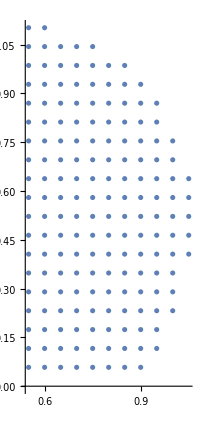

```mathematica
ComplexListPlot[z/.zvals20]
```

```mathematica
N[Table[Log[Abs[((-1/(-z+Conjugate[z])(1-z) Abs[z]^2 (1-Conjugate[z]) ((1-z)^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-z]-(1-Conjugate[z])^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,1-Conjugate[z]])+1/(z-Conjugate[z])z Abs[1-z]^2 Conjugate[z] (z^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,z]-Conjugate[z]^(1/2 (2+2 i)) Hypergeometric2F1[1/2 (2+2 i),1/2 (2+2 i),2+2 i,Conjugate[z]])))]/.zvals20[[10]]],{i,190,200}],50]
```

{-6.0795796120413325056420255932358186982204566123702,-5.3011885010557890829418842291489760697900222089352,-5.2167850008765294362974265431846576726905718959372,-6.699215938453292835811031147938341862751875926312,-5.1198034468802264961745661916174581383289651752459,-5.9110889801825174276114655281984691868393986070847,-5.5358298138428787151022215918447264361563347110874,-5.2691627805188879053054846271130848123951926243739,-7.7829830824996879533256483096378858503103316019382,-5.2623181340416384392054549022236034254945224151202,-5.8188359565925842861201096895891539679537811245333}

```mathematica
{z,confBlockExponent[z/.zvals20[[10]]]}/.zvals20[[10]]
```

{11/20+(29 ⅈ)/50,-0.03450285955148158396769028029092385910416277668658}

```mathematica
ComplexArrayPlot[{{I,1+I,1-I},{1,I/2,2+3 I}}]
```

```mathematica
Table[{z,confBlockExponent[z/.zvals20[[i]]]}/.zvals20[[i]],{i,Length[zvals20]}];
```

```mathematica
ListPlot3D[{Re[%333[[;;,1]]],Im[%333[[;;,1]]],%333[[;;,2]]}//Transpose]
```

-Graphics3D-

```mathematica
Plot3D[confBlockExponent[x+I y],{x,0,1/2},{y,-1,1}]
```

General::munfl: -2.854789650257×10^-323 (-1.3504×10^8-1.35355×10^8 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.052977680955×10^-321 (176081.-1.40708×10^8 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.893240718482×10^-319 (6.41829×10^7-6.4011×10^7 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Fit[%,{1,Δ[0]},Δ[0]]
```

224.1527317924438126532757188628391048254860261465+1.190617929224250277591836632850600813547757386329 Δ[0]

```mathematica
D[crossing4dsusy[10],C[0]]
```

(z Abs[1-z]^2 Conjugate[z] (-Log[1-z]+Log[1-Conjugate[z]]))/(z-Conjugate[z])-((1-z) Abs[z]^2 (1-Conjugate[z]) (((1-z) Log[z])/(-1+z)-((1-Conjugate[z]) Log[Conjugate[z]])/(-1+Conjugate[z])))/(-z+Conjugate[z])

```mathematica
FullSimplify[%233/.z->x+I y,x>0&&y>0]
```

(ⅈ ((-1+x)^2+y^2) (x^2+y^2) (-Log[-x+ⅈ y]-Log[1-x+ⅈ y]+Log[-1+x+ⅈ y]+Log[x+ⅈ y]))/(2 y)

```mathematica
crossing4d[10]/.z->1/2+I*2/3//Simplify
```

0

```mathematica
%233
```

(z Abs[1-z]^2 Conjugate[z] (-Log[1-z]+Log[1-Conjugate[z]]))/(z-Conjugate[z])-((1-z) Abs[z]^2 (1-Conjugate[z]) (((1-z) Log[z])/(-1+z)-((1-Conjugate[z]) Log[Conjugate[z]])/(-1+Conjugate[z])))/(-z+Conjugate[z])

```mathematica
Assuming[θ>0,Simplify[ComplexExpand[%233/.z->r Exp[I θ]]]]
```

-1/2 r (Arg[ⅇ^(ⅈ θ) r]+Arg[1-ⅇ^(ⅈ θ) r]-Arg[ⅇ^(-ⅈ θ) Conjugate[r]]-Arg[1-ⅇ^(-ⅈ θ) Conjugate[r]]) (1+r^2-2 r Cos[θ]) Csc[θ]

```mathematica
(Series[Assuming[θ>0&&r>0,Simplify[%233/.z->r Exp[I θ]]],{θ,0,0}]//Normal)/.θ->0//Simplify
```

-(r ((-1+r)^3+r Abs[1-r]^2))/(-1+r)

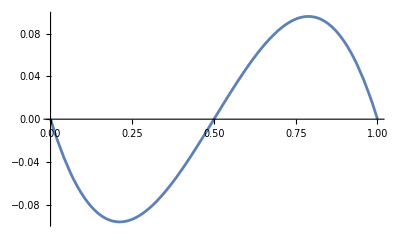

```mathematica
Plot[%290,{r,0,1}]
```

```mathematica
Simplify[(Series[%233/.z->x+I y,{y,0,0}]//Normal)/.y->0,x
```

1/(x-Conjugate[x])(x Abs[1-x]^2 Conjugate[x] (-Log[1-x]+Log[1-Conjugate[x]])-(-1+x) Abs[x]^2 (-1+Conjugate[x]) (Log[x]-Log[Conjugate[x]]))

```mathematica
Simplify[Series[%233/.z->x+I y,{y,0,0}],x>0&&0<y<1/1000]
```

(Abs[1-x-ⅈ y]^2+Abs[x+ⅈ y]^2) O[y]^0

```mathematica
%233/.z->x//Abs
```

```mathematica
Plot[%233/.z->x//Abs,{x,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Plot3D[%233/.z->x+I y//Abs,{x,0,1},{y,-1,1},AxesLabel->{x,y}]
```

-Graphics3D-